## Functions

```mathematica
ToVect[p1_,p2_]:={p2[[1]]-p1[[1]],p2[[2]]-p1[[2]],0}
IsLeft[p1_,p2_,p3_]:=If[Cross[ToVect[p1,p2],ToVect[p1,p3]][[3]]>0,True,False]
IsRight[p1_,p2_,p3_]:=If[Cross[ToVect[p1,p2],ToVect[p1,p3]][[3]]<0,True,False]
LineIntersect[p1_,p2_,p3_,p4_]:=And[IsLeft[p1,p2,p3]⊻IsLeft[p1,p2,p4],IsLeft[p3,p4,p1]⊻IsLeft[p3,p4,p2]]&&p2!=p3

BuildSimplePolygon[sideNumber_]:=(
pointsList=Table[{0,0},{i,1,sideNumber}];
For[i=1,i≤sideNumber,i++,
pointsList⟦i⟧=RandomReal[{0,20},2];
If[i>3,
For[j=1,j<i-1,j++,
If[LineIntersect[pointsList⟦i-1⟧,pointsList⟦i⟧,pointsList⟦j⟧,pointsList⟦j+1⟧],i--; Break];
If[LineIntersect[pointsList⟦1⟧,pointsList⟦i⟧,pointsList⟦j⟧,pointsList⟦j+1⟧],i--; Break];
]]])

InOrOut[P_List,P1_]:=(
P0={0,P1[[2]]};
Counter=0;
For[i=1,i<Length[P],i++,
If[LineIntersect[P1,P0,P[[i]],P[[i+1]]],Counter++;]
If[Cross[ToVect[P0,P1],ToVect[P0,P[[i]]]][[3]]==0&&P[[i,1]]≤P1[[1]],
If[!LineIntersect[P0,P1,P[[If[i-1>0,i-1,Length[P]-1]]],P[[i+1]]]&&
(Cross[ToVect[P0,P1],ToVect[P0,P[[If[i-1>0,i-1,Length[P]-1]]]]][[3]]>0&&Cross[ToVect[P0,P1],ToVect[P0,P[[i+1]]]][[3]]>0)
,Counter+=2;]
]])
```

## Lab code

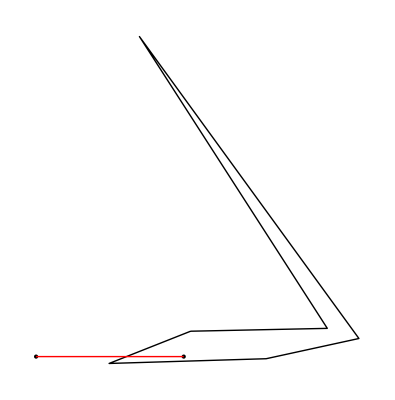

1

{8,2}

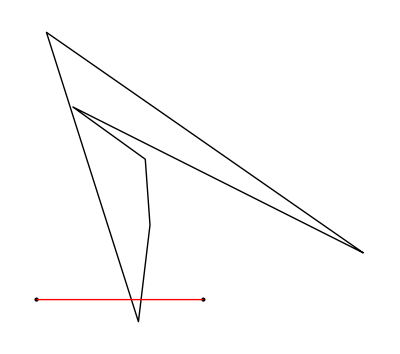

2

```mathematica
number=6;
BuildSimplePolygon[number];
P=AppendTo[pointsList,First[pointsList]];
P1={8,2};
InOrOut[P,P1];
Show[Graphics[{Line[P],Point[P1],Point[P0],Red,Line[{P0,P1}]}]]
If[Mod[Counter,2]≠0,1,0]
```

2

0

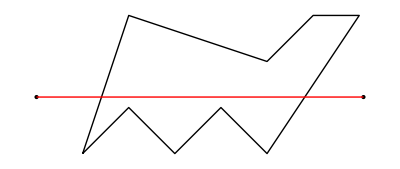

```mathematica
Counter
If[Mod[Counter,2]==1,1,0]
Show[Graphics[{Line[P],Point[P1],Point[P0],Red,Line[{P0,P1}]}]]
```